```mathematica
Clear["Combinatorica`MultipleFielderVector"]
Import["GraphPartition.m"]
<< GraphPartition`
<< Combinatorica`
$Context
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

Global`

```mathematica
ga=RoachGraph[100]
(*ShowGraph[ga]*)
```

⁃Graph:<248,200,Undirected>⁃

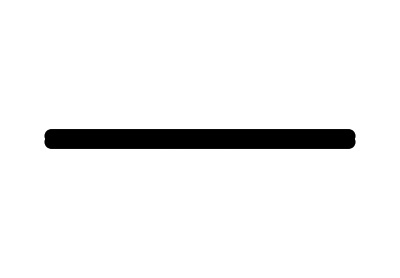

-Graphics-

-Graphics-

-Graphics-

```mathematica
GraphPartition`ShowSpectralCut[ga]
GraphPartition`ShowIsoperimetricCut[SetVertexWeights[ga,Table[1,V[ga]]]]

ShowGraph[GraphPartition`MultipleFiedlerCut[ga]]

GraphPartition`ShowMultipleFiedlerCut[ga]
```

```mathematica
ga=SetVertexWeights[ga,Table[1,V[ga]]]
EvaluatePartitionAlg[alg_,g_] := Timing[alg[g]]
VertexWeights[ga]
```

⁃Graph:<248,200,Undirected>⁃

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
EvaluatePartitionAlg[SpectralCut,ga ]
```

{0.28125,⁃Graph:<229,200,Undirected>⁃}

# Small experiments 1. Develop evaluation matrix - Runtime - ObjectiveFunction - Parameters Spectral Partitioning - Isoperimetric Partitioning -> The Ground Vertex -> The number of iterations Multiple Fiedler Vector -> The # of eigenvectors -> Spectral Vertex Choice heuristic 2. Find dataset & benchmarks -> RandomTree, RoachGraphs -> DIMACS Graph Partitioning and Graph Clustering http://www.cc.gatech.edu/dimacs10/downloads.shtml -> Chris Walshaw’s graph partitioning archive http://chriswalshaw.co.uk/partition/ http://www.cc.gatech.edu/dimacs10/archive/data/walshaw/ -> Graph partitioning training examples http://eniac.cyi.ac.cy/display/UserDoc/Graph+Partitioning+Training+Examples#GraphPartitioningTrainingExamples-Example1